Mohamed M. Hammad

Neural Network and Deep Learning with Mathematica                                < >    Ξ

Edited by Hao Feng

## 3 Matrix Calculus and Gradient Optimization

Remark: This chapter provides a Mathematica implementation of the concepts and ideas presented in Chapter 2, [1], of the book titled Artificial Neural Network and Deep Learning: Fundamentals and Theory. We strongly recommend that you begin with the theoretical chapter to build a solid foundation before exploring the corresponding practical implementation. This chapter also serves as a summary of the book titled Mathematics for Machine Learning and Data Science: Optimization with Mathematica Applications. For detailed proofs of theorems, additional examples, and comprehensive explanations, including Mathematica applications, please refer to Ref [11].”

In the realm of AI and machine learning, the modern development of NNs stands as a testament to the marriage of sophisticated mathematical frameworks and computational ingenuity. At the heart of this evolution lies the profound influence of matrix calculus [12-14] and gradient optimization techniques [15-23]. These foundational pillars have not only reshaped the landscape of NN design but have also propelled advancements in diverse domains, ranging from computer vision to natural language processing and beyond.

Matrix calculus, with its roots in linear algebra, provides a powerful toolset for analyzing and manipulating multidimensional data structures. It offers a systematic framework for computing derivatives and gradients of functions involving matrices and vectors, enabling efficient optimization in high-dimensional spaces. Matrix calculus is indeed essential for building and training NNs. NNs, especially deep learning models, heavily rely on matrix operations for their computations.

Here’s why matrix calculus is crucial for NNs:

• NNs are typically represented and implemented using matrices and vectors. Each layer in a NN can be seen as a matrix operation, where inputs (vectors) are multiplied by weights (matrices) and passed through functions (activation functions).

• The training of NNs often involves optimization algorithms like Gradient Descent (GD). Matrix calculus provides the necessary tools to compute gradients efficiently, enabling the optimization process to update the network parameters (weights) in the direction that minimizes the objective (loss) function.

• Backpropagation is the primary algorithm used to compute gradients efficiently in NNs. It is essentially an application of the chain rule from calculus, which involves matrix multiplication and transposition operations.

• Matrix calculus allows for efficient computation of derivatives and gradients in NNs. This efficiency is crucial for training deep NNs, which may have millions of parameters.

• Most deep learning frameworks handle much of the matrix calculus under the hood. However, understanding the underlying principles of matrix calculus can help in debugging, optimizing, and customizing NN architectures.

Complementing matrix calculus is the arsenal of gradient optimization techniques, which are fundamental to training NNs. By iteratively adjusting model parameters in the direction of steepest descent, these methods seek to minimize a predefined objective function, such as the loss function in supervised learning tasks. From classic algorithms like GD to more advanced variants like Stochastic Gradient Descent (SGD) and Adaptive Moment (Adam) optimization, these techniques play a pivotal role in navigating the vast landscape of model parameter space efficiently and effectively.

This chapter aims to introduce the concepts of numerical differentiation, matrix calculus, gradient optimization, and demonstrate their implementation using Mathematica.

• Numerical differentiation is a crucial technique in computational mathematics, enabling the approximation of derivatives from discrete data points. This is particularly useful when analytical differentiation is challenging or impossible.

• Matrix calculus extends traditional calculus to higher dimensions, dealing with functions that map matrices to scalars, vectors, or other matrices.

• Optimization is at the heart of machine learning, where we aim to minimize a loss (or objective) function. Gradient-based methods, such as gradient descent, iteratively adjust the parameters to reduce the loss.

By the end of this chapter, you will be able to:

• Implement matrix calculus operations in Mathematica.

• Implement numerical differentiation techniques in Mathematica.

• Utilize Mathematica to perform gradient-based optimization.

This chapter will include detailed explanations, examples, and Mathematica code snippets to ensure a comprehensive understanding of these topics.

code 3.1

(* The code demonstrates the numerical approximation of the first derivative of
the function f(x)= sin(x) at x0=Pi/4 using finite difference methods. It calculates
the forward, backward, and central difference approximations with a step size
h=0.1,and compares these results to the exact derivative obtained analytically.
The code prints the approximations and the exact derivative, and generates a plot
of the function over the interval [x_0-h,x_0+h], highlighting the point at x0
where the derivative is approximated: *)

Forward Difference Approximation: 0.670603

Backward Difference Approximation: 0.741255

Central Difference Approximation: 0.705929

Exact Derivative: 0.707107

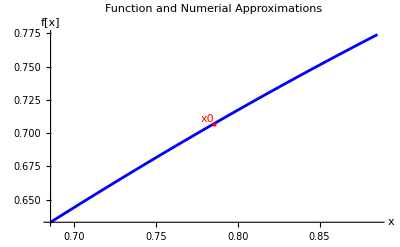

```mathematica
f[x_]:=Sin[x]
x0=π/4;
h=0.1;

forwardDifference=(f[x0+h]-f[x0])/h;
backwardDifference=(f[x0]-f[x0-h])/h;
centralDifference=(f[x0+h]-f[x0-h])/(2h);

exactDerivate=D[f[x],x]/.x->x0;

Print["Forward Difference Approximation: ",forwardDifference]
Print["Backward Difference Approximation: ",backwardDifference]
Print["Central Difference Approximation: ",centralDifference]
Print["Exact Derivative: ",N[exactDerivate]]

plotFunction=Plot[
f[x],
{x,x0-h,x0+h},
PlotStyle->Blue,
PlotLabel->"Function and Numerial Approximations",
Epilog->{
Red,
PointSize[Large],
Point[{x0,f[x0]}],
Text["x0",{x0,f[x0]},{1,-1}]
},
AxesLabel->{"x","f[x]"}
];

Show[plotFunction]
```

code 3.2

(* The goal of the `Manipulate` code is to dynamically illustrate and compare the
numerical approximations of the first derivative of the function f(x)= sin(x) at
x0=Pi/4 using finite difference methods (forward, backward, and central
differences) with a variable step size h. The code calculates these approximations
and the exact derivative, displays the results, and plots the function along with
the tangent lines corresponding to the numerical approximations. The interactive
slider allows users to adjust the step size h, providing a visual and numerical
understanding of how the step size affects the accuracy of the derivative
approximations: *)

```mathematica
Manipulate[
Module[
{f,x0,forwardDifference,backwardDifference,centralDifference,exactDerivate,plotFunction},
f[x_]:=Sin[x];
x0=π/4;

forwardDifference=(f[x0+h]-f[x0])/h;
backwardDifference=(f[x0]-f[x0-h])/h;
centralDifference=(f[x0+h]-f[x0-h])/(2h);
exactDerivate=D[f[x],x]/.x->x0;

Column[
{
Row[{"Step size (h): ",NumberForm[h,{4,2}]}],
Row[{"Forward Difference Approximation: ",NumberForm[forwardDifference,{8,6}]}],
Row[{"Backward Difference Approximation: ",NumberForm[backwardDifference,{8,6}]}],
Row[{"Central Difference Approximation: ",NumberForm[centralDifference,{8,6}]}],
Row[{"Exact Derivate: ",NumberForm[exactDerivate,{8,6}]}],
Plot[
{
f[x],
f[x0]+(x-x0)forwardDifference,
f[x0]+(x-x0)backwardDifference,
f[x0]+(x-x0)centralDifference},
{x,x0-2h,x0+2h},
PlotStyle->{Blue,Red,Green,Purple},
PlotLegends->{"f[x]","Forward Approximation","Backward Approximation","Central Approximation"},
Epilog->{
Red,
PointSize[Large],
Point[{x0,f[x0]}],
Text["x0",{x0,f[x0]},{1,-1}]
},
PlotLabel->"Function and Numerical Approximations",
AxesLabel->{"x","f[x]"},
ImageSize->300
]
}
]
],
{{h,0.1,"Step size (h)"},0.001,2,0.01}
]
```

D::dvar: Multiple derivative specifier {x1,x2,x3} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

D::ivar: π/4 is not a valid variable.

code 3.3

```mathematica
f[x_]:=x^2
D[f[x],x]
```

2 x

code 3.4

(* The code defines a scalar function f(x)=a.x, where x is a vector {x1,x2,x3}
and a is a constant vector {a1,a2,a3},representing the dot product of a and x. It
then computes the gradient of f with respect to the vector x using the `Grad`
function, resulting in the vector {a1,a2,a3},which consists of the partial
derivatives of f with respect to each component of x: *)

```mathematica
a={a1,a2,a3};
x={x1,x2,x3};
f[x_]:=a.x

Grad[f[x],x]
```

{a1,a2,a3}

code 3.5

(* The code defines a scalar function f(X)= Tr(Transpose(A). X),where X and A are
(2*2) matrices. The function computes the trace of the product of the transpose
of matrix A and matrix X. It then calculates the gradient of f with respect to
each element of the matrix X using the `Table` and `D` functions, resulting in a
(2*2) matrix where each element is the partial derivative of f with respect to
the corresponding element in X: *)

```mathematica
X={{x11,x12},{x21,x22}};
A={{a11,a12},{a21,a22}};
Tr[Transpose[A].X]

f[X_]:=Tr[Transpose[A].X]
grad=Table[D[f[X],X[[i,j]]],{i,1,2},{j,1,2}]
```

a11 x11+a12 x12+a21 x21+a22 x22

{{a11,a12},{a21,a22}}

code 3.6

(* The code defines a vector function f(x)= {x^2,x^3} and computes its derivative
with respect to x. The `D` function is used to differentiate each component of
the vector function, resulting in the vector of derivatives {2x,3x^2}: *)
(* Define the vector function f(x): *)

```mathematica
Clear[f,x];
f[x_]:={x^2,x^3}

D[f[x],x]
```

{2 x,3 x^2}

code 3.7

(* The code defines a vector function f(x_1,x_2)= {x_1^2+x_2,x_1 x_2} and computes
its Jacobian matrix with respect to the vector x= {x_1,x_2}. The `D` function is
used to differentiate each component of the vector function with respect to x_1
and x_2, resulting in the Jacobian matrix: *)

```mathematica
Clear[f,x];
f[x1_,x2_]:={x1^2+x2,x1 x2}
JacobianMatrix=D[f[x1,x2],{{x1,x2}}]
```

{{2 x1,1},{x2,x1}}

code 3.8

(* The code creates a 3D contour plot of the function x^2+y^2+z^2 over the ranges
[-2,2] for x, y, and z. The plot includes 5 contour levels and is restricted to
the region where x<0 or y>0. The contour levels are colored in Red, Orange, Yellow,
Green, and Blue: *)

```mathematica
ContourPlot3D[
x^2+y^2+z^2,
{x,-2,2},
{y,-2,2},
{z,-2,2},
Contours->5,
RegionFunction->Function[{x,y,z},x<0||y>0],
ContourStyle->{Red,Orange,Yellow,Green,Blue},
Mesh->None,
LabelStyle->Directive[Black,13],
PlotLegends->"Expressions",
ImageSize->300
]
```

-Graphics3D-

code 3.9

(* The code creates a 3D contour plot of the function x^2+y^2-z^2 over the ranges
[-3,3] for x, y, and z. The plot includes specific contour levels at -3, 0, and
3, with the contour levels colored in Red, Orange, and Yellow. The plot is
restricted to the region where x<0 or y>0 using the `RegionFunction`: *)

```mathematica
ContourPlot3D[
x^2+y^2-z^2,
{x,-3,3},
{y,-3,3},
{z,-3,3},
Contours->{-3,0,3},
ContourStyle->{Red,Orange,Yellow},
Mesh->None,
RegionFunction->Function[{x,y,z},x<0||y>0],
PlotLegends->"Expressions",
ImageSize->250
]
```

-Graphics3D-

code 3.10

(* ResourceFunction[“DirectionalDerivative”] [f,vars,pt,v] computes the
directional derivative of the function f of the variables vars at the point pt in
the direction of the normalized vector v: *)

```mathematica
ResourceFunction["DirectionalDerivativePlot3D"][
9-x^2/2-y^2/2,
{x,-2.2,2.2},
{y,-2.2,2.2},
{0,-2},
{Cos[π/4],Sin[π/4]},
ColorFunction->"SouthwestColors",
ImageSize->250
]
```

-Graphics3D-

code 3.11

```mathematica
ResourceFunction["DirectionalDerivativePlot3D"][
9-x^2/2-y^2/2,
{x,-2.2,2.2},
{y,-2.2,2.2},
{
{0,-2},{1,-1/2}
},

{{Cos[π/4],Sin[π/4]},{1,0}
},
ColorFunction->"SouthwestColors",
ImageSize->250
]
```

-Graphics3D-

Now, let’s consider a simple example to illustrate how the gradient descent method works. Mathematica codes 3.12 and 3.13 create interactive visualization demonstrating the gradient descent optimization process for a one- and two- dimensional loss function, respectively. Here’s an overview of how the Mathematica codes 3.12 achieves this goal:

• The code defines a quadratic loss function 𝐽(𝜃)=(𝜃−3)^2 +5, representing a curve in a one-dimensional space.

• The `GradientDescent` function is implemented to perform the gradient descent optimization algorithm. This function iteratively updates the parameter 𝜃 based on the gradient of the loss function until convergence or the maximum number of iterations is reached. It returns the history of parameter values during optimization.

• The `Manipulate` function from Mathematica is utilized to create an interactive interface. Users can adjust parameters such as the learning rate, initial guess for 𝜃, tolerance for convergence, and maximum iterations. The interface dynamically updates the visualization based on user inputs.

• The loss function curve 𝐽(𝜃) is plotted against the parameter 𝜃. Additionally, the optimization path taken by gradient descent is displayed as a sequence of points (red) and arrows (blue) on the plot. Users can observe and analyze how changes in the parameters influence the optimization process and its convergence towards the minimum of the loss function.

Let’s discuss how users can observe the effects on the optimization path and convergence behavior using the provided interactive visualization.

1. The learning rate determines the step size of each iteration in the gradient descent algorithm. Users can adjust the learning rate using the slider labeled “Learning Rate.” A higher learning rate may lead to faster convergence but can also cause overshooting or oscillations around the minimum. Conversely, a lower learning rate may result in slower convergence but with more stable behavior. Users can experiment with different learning rates to observe how they affect the optimization path and convergence behavior.

2. The initial guess for the parameter 𝜃 determines the starting point of the optimization process. Users can adjust the initial guess using the slider labeled “Initial Guess.” Different initial guesses may lead to different optimization paths and convergence behaviors. Users can explore how changing the initial guess influences the optimization path and convergence behavior.

3. The tolerance parameter determines the convergence criterion for the optimization process. If the absolute gradient of the loss function falls below the tolerance value, the optimization process is considered converged. Users can adjust the tolerance using the slider labeled “Tolerance.” A smaller tolerance value leads to stricter convergence criteria, potentially requiring more iterations for convergence. Users can observe how changing the tolerance affects the number of iterations and convergence behavior.

4. The maximum iterations parameter limits the number of iterations allowed for the optimization process. If the optimization process does not converge within the specified maximum iterations, it terminates. Users can adjust the maximum iterations using the slider labeled “Max Iterations.” Setting a higher maximum iterations value allows for more iterations, potentially leading to convergence even with slower convergence rates. Users can experiment with different maximum iterations settings to observe their effects on convergence behavior.

code 3.12

(* The code creates an interactive visualization demonstrating the gradient descent
optimization process for a one-dimensional loss function. A quadratic loss function
J(θ)=(θ-3)^2+5 is defined, representing a curve in a one-dimensional space. The
code implements the gradient descent optimization algorithm in the GradientDescent
function. This function iteratively updates the parameter θ based on the gradient
of the loss function until convergence or the maximum number of iterations is
reached. Users can adjust parameters like the learning rate, initial guess for θ,
tolerance for convergence, and maximum iterations. The interface dynamically
updates the visualization based on user inputs. The loss function curve J(θ) is
plotted against the parameter θ. The optimization path taken by gradient descent
is displayed as a sequence of points (red) and arrows (blue) on the plot. Users can observe and analyze how changes in the parameters influence the optimization
process and its convergence towards the minimum of the loss function: *)

```mathematica
Manipulate[
Module[
{θHistory,θOpt,minLoss},

J[θ_]:=(θ-3)^2+5;

GradientDescent[α_,θ0_,tol_,maxIter_]:=Module[
{θ=θ0,history={θ0},iter=0},
While[
iter<maxIter&&Abs[D[J[x],x]/.x->θ]>tol,
θ=θ-α D[J[x],x]/.x->θ;
AppendTo[history,θ];
iter++;
];
history
];

θHistory=GradientDescent[α,θ0,tol,maxIter];

plot=Plot[
J[θ],
{θ,-2,8},
PlotRange->All,
Epilog->{
Red,
PointSize[0.02],
Point[{#,J[#]}&/@Most[θHistory]],
Blue,
Arrowheads[0.03],
Arrow/@Partition[Thread[{Most[θHistory],J/@Most[θHistory]}],2,1]
},
PlotLabel->"Gradient Descent Optimization",
AxesLabel->{"θ","J(θ)"},
ImageSize->250
];
plot
],

{{α,0.1,"Learning Rate"},0.01,1,0.01,Appearance->"Labeled"},
{{θ0,0.0,"Initial Guess"},-2,5,0.1,Appearance->"Labeled"},
{{tol,0.0001,"Tolerance"},0.00001,0.001,0.00001,Appearance->"Labeled"},
{{maxIter,1,"Max Iterations"},1,15,1,Appearance->"Labeled"}
]
```

code 3.13

(* The code offers an interactive visualization of the gradient descent
optimization process for a quadratic loss function. A quadratic loss function,
J(x,y), is defined to represent a surface in the 2D space. This function serves
as the target for optimization. The code implements the gradient descent
optimization algorithm in the GradientDescent function. This function iteratively
updates the parameters x and y based on the gradient of the loss function, aiming
to minimize it. Users can specify parameters like the learning rate, initial
guesses for x and y, tolerance for convergence, and maximum number of iterations.
As users modify these parameters, the optimization process is visually represented
on a contour plot. The contour plot displays the loss function surface. The
optimization path taken by gradient descent is depicted as a sequence of points
(blue) and arrows (red) on this plot. Users can observe how changes in the
parameters affect the optimization process and its convergence towards the minimum
of the loss function: *)

```mathematica
J[x_,y_]:=(x-3)^2+(y-2)^2+5
GradientDescent[α_,{x0_,y0_},tol_,maxIter_]:=Module[
{x=x0,y=y0,history={{x0,y0}},iter=0,grad},
While[
iter<maxIter&&Norm[grad=D[J[xp,yp],{{xp,yp}}]/.{xp->x,yp->y}]>tol,{x,y}={x,y}-α grad;
AppendTo[history,{x,y}];
iter++;
];
history
]

Manipulate[
Module[
{history,contourPlot,arrows},
history=GradientDescent[α,{x0,y0},tol,maxIter];
contourPlot=ContourPlot[
J[x,y],
{x,-2,5},
{y,-2,5},
PlotLabel->"Gradient Descent Optimization",
AxesLabel->{"x","y"},
PlotRange->All,
Epilog->{Blue,PointSize[0.02],Point[history]},
Contours->Function[{min,max},Range[min,max,5]],
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
LabelStyle->Directive[Black,10],
ImageSize->250
];
arrows=Graphics[
{
Red,Arrowheads[0.03],
Arrow/@Partition[history,2,1]
},
PlotRange->All
];
Show[contourPlot,arrows]],
{{x0,0.0,"Initial x"},-2,5,Appearance->"Labeled"},
{{y0,0.0,"Initial y"},-2,5,Appearance->"Labeled"},
{{α,0.1,"Learning Rate"},0.01,1,Appearance->"Labeled"},
{{tol,0.0001,"Tolerance"},0.0001,0.1,Appearance->"Labeled"},
{{maxIter,1,"Max Iterations"},1,100,1,Appearance->"Labeled"},
TrackedSymbols:>{x0,y0,α,tol,maxIter}
]
```

Moreover, for many real-world optimization problems involving multivariable functions, analytical solutions may not be feasible, and numerical methods like the conjugate gradient, principal axis, Levenberg Marquardt, Newton, quasi Newton, interior point, and linear programming, are indispensable for finding approximate solutions. Each method has its advantages and limitations, and the choice of method depends on the specific characteristics of the optimization problem at hand. In the following chapters of this book, we will explore numerical optimization methods for neural networks in depth. For now, let us utilize Mathematica to implement solutions for optimization problems. We focus on the practical utilization of Mathematica’s optimization functions for optimization problems. From identifying optimal solutions to visualizing the optimization process, Mathematica equips users with powerful tools to tackle a wide array of optimization challenges efficiently and accurately.

The commands FindMinimum, NMinimize, Minimize and FindMinimumPlot can do optimization for both single- variable and multivariable functions.

code 3.14

(* The code snippets demonstrate various applications of the `MinValue` function.
The first snippet finds the minimum value of a univariate function 4x^4-5x^2+7 with
respect to x. The second snippet extends this to a multivariate function x^2+y^2-
4)^2+2,finding the minimum value with respect to both x and y. The third snippet
introduces a constraint, determining the minimum value of x^2+3y subject to
x^2+y^2<=4. Finally, the fourth snippet finds the minimum value of a parameterized
function bx^3+ax^2+cx+d with respect to x, returning the result as a function of
the parameters a, b, c, and d: *)

```mathematica
Clear[a,b,c,d,x];

MinValue[4 x^4-5 x^2+7,x]
MinValue[(x^2+y^2-4)^2+2,{x,y}]
MinValue[{x^2+3 y,x^2+y^2<=4},{x,y}]
MinValue[b x^3+a x^2+c x+d,x]
```

87/16

2

-6

Piecewise[{{d, c==0&&a≥0&&b==0}, {(-c^2+4 a d)/(4 a), (c>0&&a>0&&b==0)||(c<0&&a>0&&b==0)}, {-∞, True}}]

code 3.15

(* The code snippets utilize the `NMinValue` function to find global minimum values
in different scenarios. The first snippet computes the global minimum value of the
univariate function 4x^4-5x^2+7 with respect to x. The second snippet extends this
to a multivariate function x^2+y^2-4)^2+2,determining the global minimum value with
respect to both x and y. The third snippet introduces a constraint, finding the
global minimum value of x^2+3y subject to the constraint x^2+y^2<=4 with respect to
x and y: *)

```mathematica
NMinValue[4 x^4-5 x^2+7,x]
NMinValue[(x^2+y^2-4)^2+2,{x,y}]
NMinValue[{x^2+3 y,x^2+y^2<=4},{x,y}]
```

5.4375

2.

-6.

code 3.16

(* The code snippets use `FindMinValue` to locate minimum values under different
conditions: the first snippet finds a minimum value of the univariate function 4x^4-
5x^2+7 with respect to x; the second snippet finds a minimum value of the
multivariate function x^2+y^2-4)^2+2 with respect to both x and y; and the third
snippet finds a minimum value of the function x^2+3y subject to the constraint
x^2+y^2<= 4 with respect to x and y: *)

```mathematica
FindMinValue[4 x^4-5 x^2+7,x]
FindMinValue[(x^2+y^2-4)^2+2,{x,y}]
FindMinValue[{x^2+3 y,x^2+y^2<=4},{x,y}]
```

5.4375

2.

-6.

code 3.17

(* The code snippets use `ArgMin` to find minimizer points in various scenarios:
the first snippet identifies the minimizer point of the univariate function 4x^4-
5x^2+7 with respect to x; the second snippet determines the minimizer point of the
multivariate function x^2+y^2-4)^2+2 with respect to x and y; the third snippet
locates the minimizer point of the function x^2+3y subject to the constraint x^2+y^2
<= 4 with respect to x and y; and the fourth snippet finds the minimizer point of
the parameterized function ax^2+bx+c with respect to x, expressed as a function of
the parameters a, b, and c: *)

```mathematica
ArgMin[4 x^4-5 x^2+7,x]
ArgMin[(x^2+y^2-4)^2+2,{x,y}]
ArgMin[{x^2+3 y,x^2+y^2<=4},{x,y}]
ArgMin[a x^2+b x+c,x]
```

-(√(5/2))/2

{0,-2}

{0,-2}

Piecewise[{{-b/(2 a), (b>0&&a>0)||(b<0&&a>0)}, {0, (b==0&&a==0)||(b==0&&a>0)}, {Indeterminate, True}}]

code 3.18

```mathematica
NArgMin[4 x^4-5 x^2+7,x]
NArgMin[(x^2+y^2-4)^2+2,{x,y}]
NArgMin[{x^2+3 y,x^2+y^2<=4},{x,y}]
```

0.790569

{1.15892,1.63}

{0.,-2.}

code 3.19

```mathematica
FindArgMin[4 x^4-5 x^2+7,x]
FindArgMin[(x^2+y^2-4)^2+2,{x,y}]
FindArgMin[{x^2+3 y,x^2+y^2<=4},{x,y}]
```

{0.790569}

{1.41421,1.41421}

{0.,-2.}

code 3.20

(* The code defines the function f(x,y)= sin(x)cos(y) and achieves several goals:
it calculates the minimum value of f(x,y) over the rectangle [0,0] to
[1,1],identifies the location (minimizer point) where this minimum occurs, and
creates a 3D plot of the function with the minimum point highlighted. Additionally,
it generates a contour plot to visualize the function in 2D, marking and labeling
the minimum value location. These visualizations help in understanding the
function’s behavior and the position of its minimum value within the specified
domain: *)

-Graphics3D-

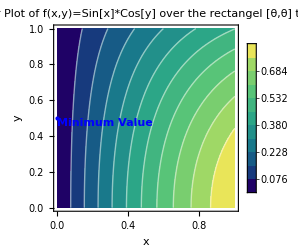

```mathematica
Clear[f];

f[x_,y_]:=Sin[x]*Cos[y]

minValue=MinValue[
f[x,y],
{x,y}∈Rectangle[{0,0},{1,1}]
];

minPoint=ArgMin[
f[x,y],
{x,y}∈Rectangle[{0,0},{1,1}]
];

minPoint3D={minPoint[[1]],minPoint[[2]],f[minPoint[[1]],minPoint[[2]]]};

Show[
Plot3D[
f[x,y],
{x,0,1},
{y,0,1},
PlotRange->All,
AxesLabel->{"x","y","f(x,y)"},
PlotLabel->"Plot of f(x,y)=Sin[x]*Cos[y] over \n the rectangel [θ,θ] to [1,1]",
ColorFunction->"BlueGreenYellow",
Mesh->None,
ImageSize->250
],
Graphics3D[
{
Blue,
PointSize[Large],
Point[minPoint3D],
Text[Style["Minimum Value",Blue,Bold],minPoint3D,{-1,1}]
}
]
]

ContourPlot[
f[x,y],
{x,0,1},
{y,0,1},
Contours->10,
ContourStyle->{White},
ClippingStyle->Automatic,
ColorFunction->"BlueGreenYellow",
PlotLegends->Automatic,
Epilog->{
Blue,
PointSize[Large],
Point[{minPoint[[1]],minPoint[[2]]}],
Text[Style["Minimum Value",Blue,Bold],{minPoint[[1]],minPoint[[2]]},{-1,1}]
},
FrameLabel->{"x","y"},
PlotLabel->"Contour Plot of f(x,y)=Sin[x]*Cos[y] over \n the rectangel [θ,θ] to [1,1]",
ImageSize->250
]
```

code 3.21

```mathematica
Minimize[4 x^4-5 x^2+7,x]
Minimize[(x^2+y^2-4)^2+2,{x,y}]
Minimize[{x^2+3 y,x^2+y^2<=4},{x,y}]
Minimize[b x^3+a x^2+c x+d,x]
```

{87/16,{x→-(√(5/2))/2}}

{2,{x→0,y→-2}}

{-6,{x→0,y→-2}}

{Piecewise[{{d, (c==0&&a==0&&b==0)||(c==0&&a>0&&b==0)}, {(-c^2+4 a d)/(4 a), (c>0&&a>0&&b==0)||(c<0&&a>0&&b==0)}, {-∞, True}}],{x→Piecewise[{{-c/(2 a), (c>0&&a>0&&b==0)||(c<0&&a>0&&b==0)}, {0, (c==0&&a==0&&b==0)||(c==0&&a>0&&b==0)}, {Indeterminate, True}}]}}

### optimization